```mathematica
Line[]
```

Line[]

```mathematica
Graphics[Line[]]
```

-Graphics-

Line[{{0,0},{1,0},{2,0},{3,0}}]

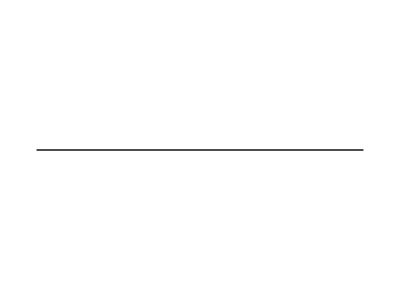

```mathematica
line =Line[{{0,0}, {1,0},{2, 0}, {3, 0}}]

graphline = Graphics[line]
```

```mathematica
bisector = PerpendicularBisector[line]
```

InfiniteLine[{3/2,0},{0,-3}]

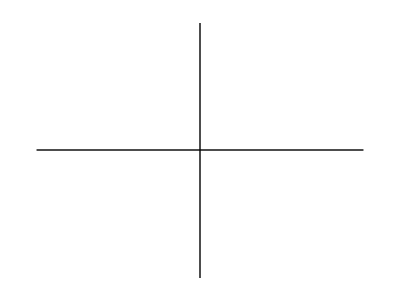

```mathematica
Graphics[{line, bisector}]
```

```mathematica
a = Line[{{1, 0}, {2, 0}}]
```

Line[{{1,0},{2,0}}]

```mathematica
Graphics[a]
```

-Graphics-

```mathematica
hat [x_, y_, theta_]:= AnglePath[{{x, y},theta},{Pi/3}]
```

```mathematica
hat[1, 0, 0]
```

{{1,0},{3/2,(√3)/2}}

```mathematica
repl[n_/;n>1,num_]:=Line[{p1_,p2_}]:>With[{pts=Take[#,Min[num,Length[#]]]&@Table[p1+i (p2-p1),{i,0,1,1.0/n}]}
```

```mathematica
repl[5, 10]
```

repl[5,10]

```mathematica
x=y=Subdivide[4,5]
```

{0,4/5,8/5,12/5,16/5,4}

```mathematica
x
```

{0,4/5,8/5,12/5,16/5,4}

```mathematica
y
```

```mathematica
{0,4/5,8/5,12/5,16/5,4}
```

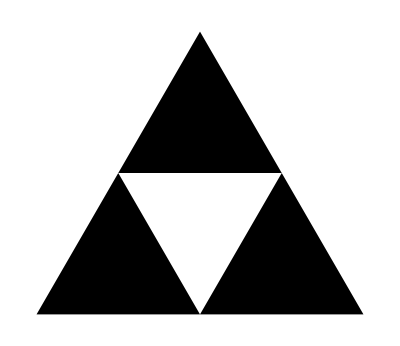

```mathematica
Graphics[SierpinskiMesh[1]]
```

```mathematica
0
```

0

```mathematica
Manipulate[
Graphics[SierpinskiMesh[u]],{u,0, 5, 1}]
```

```mathematica
pts = {{0,0}, {1, 1}}
```

{{0,0},{1,1}}

Line[{{0,0},{1,1}}]

```mathematica
newpt1 = {4/9, 2/3}
newpt2 = {5/9, 1/3}
```

{4/9,2/3}

{5/9,1/3}

```mathematica
pts = Insert[pts, newpt1, 2]
pts = Insert[pts, newpt2, 3]
```

{{0,0},{4/9,2/3},{1,1}}

{{0,0},{4/9,2/3},{5/9,1/3},{1,1}}

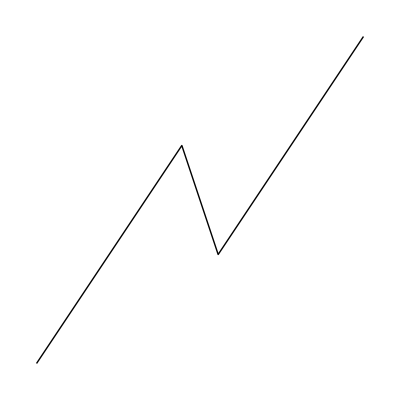

```mathematica
Graphics[Line[pts]]
```

```mathematica
ArrayReshape[Insert[pts,{newpt1,newpt2},2],4]
```

{0,0,2/3,4/9}

```mathematica
ArrayReshape[Insert[pts,{newpt1,newpt2},2],RawBoxes[RowBox[{"0",","," ","4"}]]]
```

ArrayReshape::ilsmn: Single or list of non-negative machine-sized integers expected at position 0, 4 of ArrayReshape[{{0,0},{{2/3,4/9},{1/3,5/9}},{1,1}},0, 4].

ArrayReshape[{{0,0},{{2/3,4/9},{1/3,5/9}},{1,1}},0, 4]

```mathematica
Flatten[{{0,0},{{2/3,4/9},{1/3,5/9}},{1,1}}]
```

```mathematica
{0,0,2/3,4/9,1/3,5/9,1,1}
Point[{0, 0}]
```

{0,0,2/3,4/9,1/3,5/9,1,1}

Point[{0,0}]

```mathematica
Point[{0,0}]
```

Point[{0,0}]

```mathematica
Graphics[%]
```

-Graphics-

```mathematica
Off[General::spell];Off[General::spell1];
Manipulate[
{a,b}=N[{4/9,2/3}];{c,d}=N[{5/9,1/3}];(*These are the turning points*){dx[1],dy[1]}={a,b};{dx[2],dy[2]}={c-a,d-b};{dx[3],dy[3]}={1-c,1-d};ptlst={{0,0},{a,b},{c,d},{1,1}};
Do[{newptlst={},Do[{{x1,y1}=ptlst[[j]],{x2,y2}=ptlst[[j+1]],delx=x2-x1,dely=y2-y1,{nx1,ny1}={x1,y1}+{delx*dx[1],dely*dy[1]},{nx2,ny2}={nx1,ny1}+{delx*dx[2],dely*dy[2]},newptlst=Flatten[{newptlst,{x1,y1},{nx1,ny1},{nx2,ny2}}]},{j,1,Length[ptlst]-1}],ptlst=Partition[Flatten[{newptlst,{1,1}}],2]},{i,1,iters}];Show[Graphics[Line[ptlst]],PlotRange->All,AspectRatio->1/2.5]
, {iters, 0, 6, 1}]
```

Part::partw: Part 206 of {{0,0},{0.0877915,0.296296},{0.109739,0.148148},{0.197531,0.444444},{0.219479,0.296296},{0.224966,0.37037},{0.246914,0.222222},{0.334705,0.518519},{0.356653,0.37037},{0.444444,0.666667},«18»} does not exist.

Set::shape: Lists {x1,y1} and {{0,0},{0.0877915,0.296296},{0.109739,0.148148},{0.197531,0.444444},{0.219479,0.296296},{0.224966,0.37037},{0.246914,0.222222},{0.334705,0.518519},{0.356653,0.37037},{0.444444,0.666667},«18»}⟦206⟧ are not the same shape.

Part::partw: Part 207 of {{0,0},{0.0877915,0.296296},{0.109739,0.148148},{0.197531,0.444444},{0.219479,0.296296},{0.224966,0.37037},{0.246914,0.222222},{0.334705,0.518519},{0.356653,0.37037},{0.444444,0.666667},«18»} does not exist.

Set::shape: Lists {x2,y2} and {{0,0},{0.0877915,0.296296},{0.109739,0.148148},{0.197531,0.444444},{0.219479,0.296296},{0.224966,0.37037},{0.246914,0.222222},{0.334705,0.518519},{0.356653,0.37037},{0.444444,0.666667},«18»}⟦207⟧ are not the same shape.

Part::partw: Part 207 of {{0,0},{0.0877915,0.296296},{0.109739,0.148148},{0.197531,0.444444},{0.219479,0.296296},{0.224966,0.37037},{0.246914,0.222222},{0.334705,0.518519},{0.356653,0.37037},{0.444444,0.666667},«18»} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Set::shape: Lists {x1,y1} and {{0,0},{0.0877915,0.296296},{0.109739,0.148148},{0.197531,0.444444},{0.219479,0.296296},{0.224966,0.37037},{0.246914,0.222222},{0.334705,0.518519},{0.356653,0.37037},{0.444444,0.666667},«18»}⟦207⟧ are not the same shape.

General::stop: Further output of Set::shape will be suppressed during this calculation.

```mathematica
g
```

```mathematica
Off[General::spell];Off[General::spell1];(*number of iterations-no higher than 10,unless you are very patient*)
Manipulate[
SeedRandom[164331];(*Rerunning the program with the same random number seed produces the same picture.Change the seed for a different picture.*)

{a,b}=N[{4/9,2/3}];{c,d}=N[{5/9,1/3}];(*These are the turning points*)
{dx[1],dy[1]}={a,b};{dx[2],dy[2]}={c-a,d-b};{dx[3],dy[3]}={1-c,1-d};ptlst={{0,0},{a,b},{c,d},{1,1}};permlst=Permutations[{1,2,3}];Do[{newptlst={},Do[{{x1,y1}=ptlst[[j]],{x2,y2}=ptlst[[j+1]],delx=x2-x1,dely=y2-y1,tk=Random[Integer,{1,6}],ind1=permlst[[tk]][[1]],ind2=permlst[[tk]][[2]],{nx1,ny1}={x1,y1}+{delx*dx[ind1],dely*dy[ind1]},{nx2,ny2}={nx1,ny1}+{delx*dx[ind2],dely*dy[ind2]},newptlst=Flatten[{newptlst,{x1,y1},{nx1,ny1},{nx2,ny2}}]},{j,1,Length[ptlst]-1}],ptlst=Partition[Flatten[{newptlst,{1,1}}],2]},{i,1,iters}];Show[Graphics[Line[ptlst]],PlotRange->All,AspectRatio->1/2.5]
, {iters, 0, 6, 1}]
```

```mathematica
Grid
```

Grid

```mathematica
His
```

ParetoDistribution::argb: ParetoDistribution called with 0 arguments; between 2 and 4 arguments are expected.

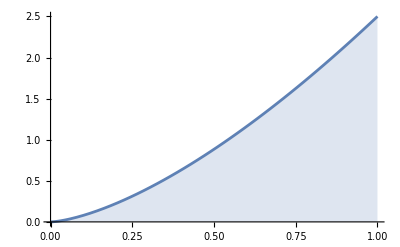

```mathematica
Plot[Table[PDF[PowerDistribution[k,2.5],x],{k,1}]//Evaluate,{x,0,1},Filling->Axis, ]
```

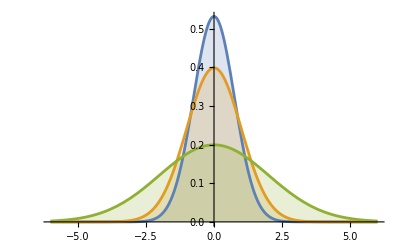

```mathematica
Plot[Table[PDF[NormalDistribution[0,σ],x],{σ,{.75,1,2}}]//Evaluate,{x,-6,6},Filling->Axis]
```

```mathematica
data = RandomVariate[PowerDistribution[1, 2.5], 10^3]
```

{0.686209,0.979748,0.726955,0.629424,0.837969,0.461757,0.790024,0.753807,0.825786,0.944091,0.660296,0.77424,0.567849,0.27151,0.64276,0.851133,0.898112,0.389915,0.388066,0.589823,0.931704,0.97809,0.660724,0.752938,0.388877,0.771894,0.895168,0.644895,0.909422,0.582057,0.969412,0.897824,0.13877,0.979548,0.693698,0.536472,0.62239,0.725989,0.453779,0.476309,0.918627,0.720416,0.615362,0.810173,0.804587,0.318027,0.797735,0.899937,0.495263,0.880829,0.363035,0.420192,0.820547,0.876546,0.650966,0.818367,0.956262,0.72245,0.455545,0.566991,0.755908,0.939099,0.740574,0.95622,0.987813,0.591276,0.626649,0.825481,0.809939,0.697389,0.951392,0.640371,0.534561,0.690214,0.82875,0.738356,0.556522,0.951103,0.153852,0.779556,0.729225,0.931148,0.641344,0.9994,0.771584,0.85616,0.839038,0.540078,0.825692,0.989985,0.567432,0.979119,0.256132,0.459838,0.823049,0.732975,0.975599,0.819379,0.826701,0.493229,0.727069,0.607427,0.56556,0.739579,0.824619,0.723889,0.929228,0.788328,0.951687,0.760232,0.490622,0.64312,0.768058,0.177833,0.994059,0.788233,0.629328,0.855849,0.337463,0.764634,0.871781,0.820131,0.556741,0.911403,0.245175,0.557385,0.909251,0.460334,0.951009,0.795036,0.870848,0.465891,0.726886,0.512365,0.586566,0.778531,0.710305,0.228845,0.938276,0.656845,0.703414,0.91247,0.353115,0.738553,0.717914,0.672681,0.883072,0.872051,0.851137,0.112202,0.568435,0.877186,0.578985,0.505858,0.772753,0.946413,0.998335,0.911949,0.971502,0.754032,0.998115,0.871549,0.997632,0.721831,0.766607,0.712165,0.851854,0.644338,0.916655,0.495356,0.817788,0.813465,0.777496,0.3973,0.879394,0.453395,0.73339,0.954977,0.701615,0.157638,0.725352,0.935327,0.690156,0.999423,0.297253,0.260717,0.903064,0.506666,0.752298,0.98934,0.235269,0.678281,0.432887,0.478636,0.890068,0.70436,0.871545,0.606545,0.748458,0.887338,0.391259,0.783507,0.384452,0.373547,0.543073,0.593635,0.574658,0.466233,0.814134,0.96246,0.662834,0.86625,0.8691,0.822111,0.972881,0.989125,0.955134,0.821688,0.917876,0.889472,0.570136,0.608196,0.828379,0.71192,0.962517,0.688455,0.87315,0.978803,0.553716,0.775104,0.734997,0.561807,0.995414,0.50423,0.838209,0.673313,0.630057,0.623528,0.584212,0.999481,0.90537,0.986891,0.988334,0.683262,0.908023,0.60446,0.852811,0.804904,0.628696,0.996141,0.657371,0.553109,0.598106,0.970874,0.667817,0.930781,0.619514,0.612709,0.998473,0.677519,0.248613,0.51341,0.758312,0.939406,0.537956,0.410009,0.902128,0.673819,0.0220365,0.954461,0.831391,0.991119,0.756138,0.782851,0.869093,0.960259,0.972769,0.628974,0.515782,0.547959,0.601863,0.384516,0.244794,0.792638,0.781798,0.940776,0.681518,0.350612,0.722657,0.855732,0.970639,0.908208,0.962824,0.590689,0.998952,0.487605,0.831318,0.96799,0.742085,0.706733,0.595933,0.628314,0.466997,0.582085,0.34362,0.824523,0.498264,0.794875,0.787036,0.825232,0.853856,0.45039,0.98515,0.296862,0.819303,0.562554,0.773753,0.578837,0.445008,0.0546482,0.920167,0.610628,0.885458,0.997244,0.873478,0.540878,0.936049,0.923499,0.404817,0.795554,0.722401,0.659348,0.333798,0.83871,0.971664,0.875965,0.873383,0.547085,0.902731,0.856219,0.421705,0.637795,0.846687,0.806051,0.53504,0.911916,0.765585,0.946839,0.403118,0.997749,0.948505,0.794796,0.680423,0.925846,0.729224,0.845853,0.549975,0.690836,0.328268,0.632497,0.96783,0.0689249,0.886791,0.821916,0.927691,0.701208,0.803758,0.85512,0.590658,0.572579,0.794322,0.933496,0.625104,0.873745,0.534748,0.889822,0.885753,0.450014,0.883818,0.325653,0.890132,0.968784,0.16195,0.992768,0.82655,0.955291,0.178894,0.867543,0.701935,0.780909,0.441141,0.977408,0.756184,0.895834,0.741035,0.696062,0.955437,0.404574,0.36176,0.777949,0.338211,0.6382,0.786954,0.981628,0.727375,0.90373,0.80157,0.458109,0.910099,0.963218,0.179347,0.86569,0.637845,0.932739,0.614781,0.544052,0.771316,0.698629,0.686107,0.97552,0.479718,0.634916,0.995624,0.375392,0.972353,0.61489,0.788687,0.699212,0.929089,0.158079,0.442709,0.167009,0.416106,0.721577,0.69965,0.693155,0.966302,0.400698,0.9141,0.624482,0.747954,0.976816,0.591772,0.515899,0.662805,0.343407,0.320732,0.944894,0.70406,0.891917,0.905116,0.527985,0.942258,0.918397,0.800915,0.964064,0.433088,0.868134,0.977686,0.695104,0.970183,0.625932,0.87395,0.904255,0.930182,0.949906,0.943852,0.395365,0.991079,0.724463,0.417116,0.243374,0.757594,0.577394,0.984439,0.849408,0.516918,0.731765,0.89386,0.996311,0.893257,0.160208,0.787229,0.930925,0.599665,0.943891,0.867554,0.605732,0.781274,0.937378,0.535084,0.840423,0.937983,0.92434,0.548829,0.969871,0.430358,0.779635,0.898416,0.60331,0.412325,0.463882,0.355463,0.546678,0.546912,0.898542,0.694805,0.580339,0.525401,0.951438,0.514851,0.336019,0.878728,0.7889,0.771526,0.888446,0.924699,0.956628,0.539077,0.881309,0.635722,0.642015,0.425609,0.99296,0.758929,0.922792,0.729364,0.888575,0.67243,0.374079,0.829327,0.843784,0.979273,0.932985,0.602398,0.992659,0.962533,0.793691,0.79639,0.969181,0.504458,0.240745,0.977069,0.629939,0.810388,0.937771,0.703735,0.837634,0.267646,0.970785,0.965724,0.717143,0.855005,0.858663,0.992652,0.852194,0.592312,0.754682,0.6428,0.851397,0.895237,0.550085,0.876781,0.320282,0.715425,0.643386,0.490644,0.940889,0.768896,0.899348,0.0534753,0.709223,0.640833,0.874401,0.94868,0.733874,0.764829,0.21481,0.812268,0.94586,0.661263,0.836873,0.559933,0.547786,0.88871,0.953837,0.808484,0.890366,0.973601,0.481731,0.62048,0.686176,0.312402,0.857189,0.877807,0.567926,0.870367,0.443062,0.941172,0.762724,0.784262,0.939935,0.799364,0.954476,0.664479,0.864256,0.633429,0.6228,0.8069,0.8467,0.759559,0.965168,0.993706,0.652692,0.76909,0.670964,0.962762,0.835966,0.527244,0.882966,0.744165,0.319383,0.599434,0.716272,0.577156,0.72335,0.983338,0.840906,0.725499,0.915701,0.545219,0.975919,0.833073,0.706154,0.732386,0.152452,0.999374,0.660414,0.954901,0.0750666,0.749091,0.55192,0.598564,0.999784,0.503877,0.477772,0.65879,0.880371,0.715543,0.875512,0.637628,0.708352,0.999741,0.70841,0.707015,0.983563,0.606434,0.752678,0.544079,0.923431,0.37006,0.93064,0.647043,0.92287,0.65004,0.576506,0.507861,0.941051,0.787159,0.978939,0.209739,0.31018,0.678899,0.682454,0.400203,0.305104,0.266851,0.63732,0.425743,0.680628,0.853648,0.936734,0.420399,0.0791439,0.815948,0.961634,0.964074,0.462526,0.856464,0.628741,0.411148,0.486217,0.439189,0.824034,0.585496,0.63044,0.939474,0.877915,0.673976,0.260682,0.989173,0.311073,0.694894,0.768745,0.913177,0.529137,0.629311,0.748484,0.247784,0.890835,0.630747,0.927286,0.870407,0.99335,0.567131,0.470842,0.942918,0.859306,0.909762,0.348551,0.412304,0.654872,0.439491,0.902539,0.871304,0.488543,0.848346,0.324646,0.32061,0.978176,0.917493,0.887538,0.51299,0.476192,0.656368,0.93193,0.133341,0.925747,0.856655,0.592149,0.760941,0.313279,0.82328,0.570211,0.834274,0.583192,0.90093,0.725336,0.47512,0.897626,0.984825,0.947668,0.600977,0.484691,0.976578,0.830337,0.572082,0.316997,0.721862,0.285193,0.97114,0.795666,0.975256,0.946925,0.902053,0.981805,0.917503,0.354513,0.396103,0.758965,0.768206,0.931528,0.852753,0.598441,0.676163,0.675492,0.278744,0.970855,0.179552,0.82762,0.823645,0.957306,0.964976,0.898428,0.69216,0.691402,0.86811,0.827835,0.555294,0.726067,0.665681,0.604692,0.991157,0.951252,0.79668,0.755548,0.673907,0.585688,0.954874,0.905053,0.910939,0.902588,0.730933,0.779688,0.232261,0.788201,0.914808,0.949015,0.851848,0.958577,0.473676,0.944292,0.587295,0.651422,0.751427,0.914078,0.799325,0.77535,0.753549,0.308193,0.852544,0.84995,0.829501,0.889504,0.755021,0.899418,0.817726,0.534172,0.997221,0.531687,0.341591,0.541115,0.899231,0.603626,0.959395,0.862731,0.858027,0.967181,0.754087,0.747674,0.487068,0.986935,0.464078,0.293547,0.775291,0.989301,0.924725,0.785518,0.663322,0.866815,0.90324,0.436085,0.974653,0.664209,0.987677,0.732328,0.314033,0.873696,0.811729,0.79122,0.938898,0.816314,0.784013,0.424763,0.574669,0.822349,0.878666,0.441533,0.520367,0.854477,0.26053,0.841984,0.998824,0.821671,0.962217,0.895054,0.857605,0.968748,0.803487,0.823041,0.676369,0.708129,0.818573,0.664676,0.991939,0.895024,0.326427,0.677892,0.769077,0.474816,0.764666,0.97759,0.948667,0.775539,0.704148,0.951139,0.926137,0.752003,0.745469,0.79324,0.612122,0.463056,0.95197,0.607637,0.96972,0.461132,0.988773,0.900142,0.96,0.971913,0.818223,0.802929,0.812644,0.951068,0.604528,0.803012,0.831923,0.88393,0.352231,0.034846,0.568179,0.89629,0.822024,0.34846,0.83409,0.76966,0.621917,0.851811,0.385373,0.282946,0.97086,0.941706,0.413096,0.654841,0.499361,0.802119,0.45784,0.3875,0.258158,0.447586,0.898548,0.543814,0.448823,0.933361,0.975758,0.60752,0.797213,0.992189,0.496604,0.795837,0.658535,0.999118,0.988051,0.819114,0.864908,0.668983,0.4032,0.995585,0.991878,0.837528,0.947558,0.60097,0.771426,0.719508,0.944505,0.897364,0.840947,0.848272,0.762616,0.475923,0.881962,0.819616,0.824889,0.804369,0.667223,0.408133,0.920874,0.708567,0.477122,0.575235,0.967251,0.69898,0.985562,0.84573,0.586255,0.937158,0.924707,0.637915,0.59845,0.897418,0.690838,0.671733,0.414664,0.796874,0.727829,0.681387,0.669614,0.325558,0.790455,0.721525}

```mathematica
Plot[PDF[PowerDistribution[1, 3], x], {x, -9, 9},
```

```mathematica
]
```

```mathematica
Mean[PowerDistribution[1, 3]]
```

3/4

```mathematica
PowerDistribution[1, 3]
```

PowerDistribution[1,3]

```mathematica
Plot[PDF[PowerDistribution[1, 3]
```

```mathematica
Plot[PDF[PowerDistribution[1, 3]], {x, -9, 9}]
```

-Graphics-

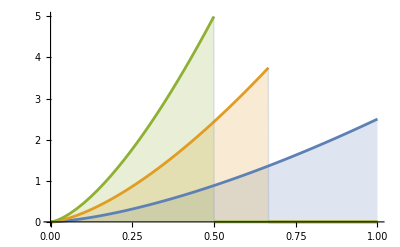

```mathematica
Plot[Table[PDF[PowerDistribution[k, 2.5], x], {k, {1, 1.5, 2}}] // 
  Evaluate, {x, 0, 1}, Filling -> Axis]
```

{2.57125,1.0358,9.68039,3.65027,1.38343,1.67823,1.04203,1.39377,1.37326,3.24777,1.70101,2.29532,2.58545,1.65333,1.37904,1.71348,1.13013,1.48647,1.08603,1.57915,3.27659,2.08696,1.55242,17.782,1.00998,1.48677,2.16374,1.2962,6.11349,1.56403}

{2.3589,3.45678,3.30009,3.4269,2.53832,3.49653,3.48029,1.40568,4.29162,2.6692,3.37266,0.762395,2.11219,2.80466,3.89741,2.69193,3.68496,3.78427,3.02502,2.62009,2.97534,2.8981,1.96316,2.55267,3.30793,2.17706,3.90963,3.51709,3.96543,4.32855}

3.

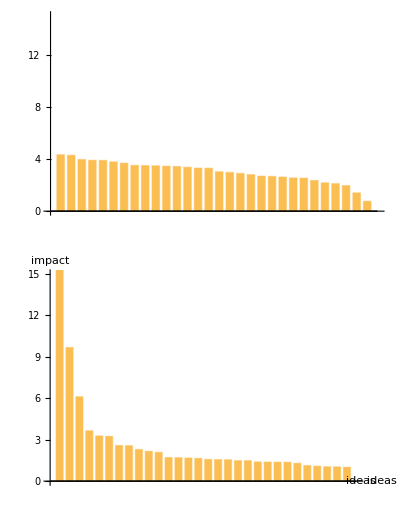

```mathematica
data = Table[RandomVariate[ParetoDistribution[1, 1.5]], 30]
gaussdata = Table[RandomVariate[NormalDistribution[3, 1]], 30]
Mean[ParetoDistribution[1, 1.5]]
GraphicsColumn[{BarChart[ReverseSort[gaussdata], PlotRange -> {Automatic, {0, 15}}],
 BarChart[ReverseSort[data], AxesLabel->{ideas, impact}, PlotRange -> {Automatic, {0, 15}}]}]
```

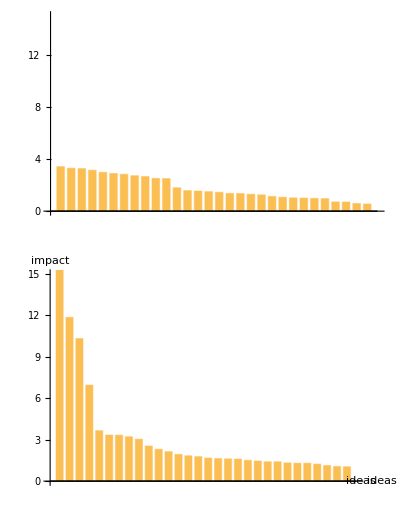

```mathematica
GraphicsColumn[{BarChart[ReverseSort[gaussdata], PlotRange -> {Automatic, {0, 15}}],Style["Mediocristan", 12],
BarChart[ReverseSort[data], AxesLabel->{Style["Ideas", 10], Style["Impact", 10]}, PlotRange -> {Automatic, {0, 15}}], Style["Extremistan", 12]}]
```

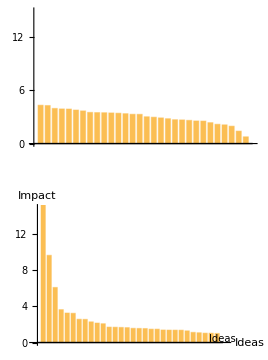

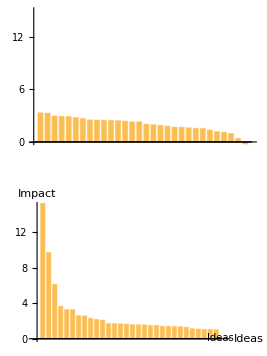

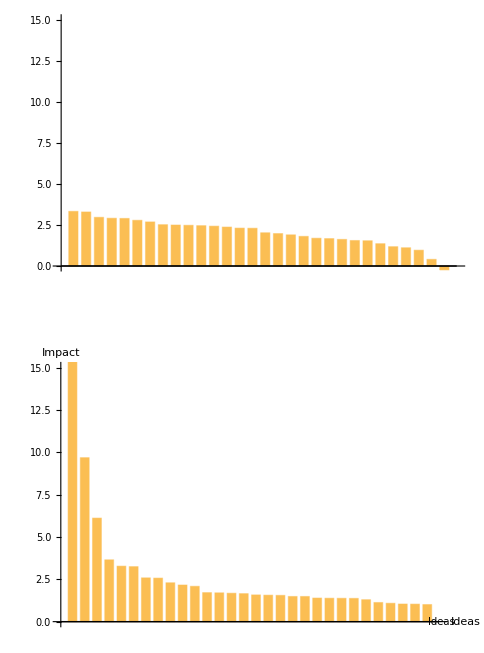

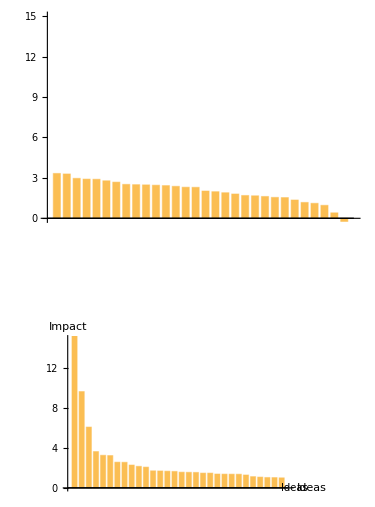

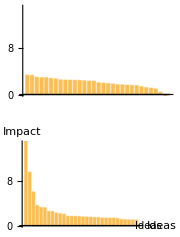

```mathematica
Show[%389,ImageSize->Small]
```

```mathematica
Show[%385,ImageSize->Small]
```

-Graphics-

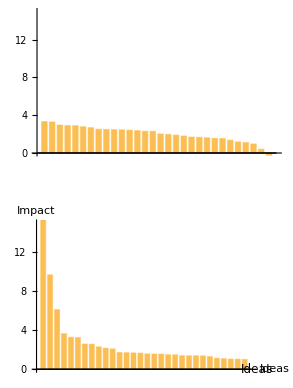

```mathematica
Show[%380,ImageSize->{293,388},AspectRatio->Full]
```

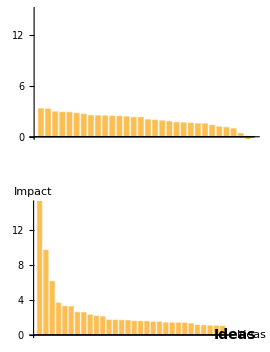

```mathematica
Show[%378,ImageSize->{270,352},AspectRatio->Full]
```

```mathematica
Show[%375,ImageSize->Medium]
```

```mathematica
Show[%376,ImageSize->Small]
```

```mathematica
\
```

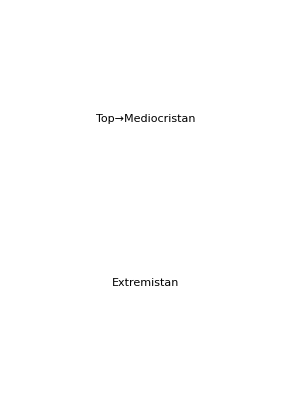

-Graphics-

```mathematica
Show[%357,ImageSize->Large]
```

```mathematica
ResourceFunction["DarkMode"][False]
```

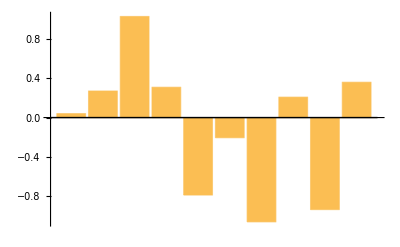

```mathematica
BarChart[Table[RandomVariate[ExponentialPowerDistribution[20]], 10]]
```

```mathematica
Mean[ExponentialPowerDistribution[5]]
```

0